### Equations

```mathematica
H=1/2(p1^2+p2^2)+1/2 q1^2+1/2 q2^2+(q1^2 q2-1/3 q2^3)//Simplify
𝕩={q1,q2,p1,p2};
Ω=({{0, 1}, {-1, 0}})~KroneckerProduct~IdentityMatrix[2];
𝒱=Ω.D[H,{𝕩}]
```

1/6 (3 p1^2+3 p2^2+3 q1^2+6 q1^2 q2+3 q2^2-2 q2^3)

{p1,p2,1/6 (-6 q1-12 q1 q2),1/6 (-6 q1^2-6 q2+6 q2^2)}

```mathematica
eq=Thread[Dt[𝕩,t]==𝒱/.a:Alternatives@@𝕩:>a[t]]//FullSimplify
```

{p1[t]==q1'[t],p2[t]==q2'[t],q1[t]+2 q1[t] q2[t]+p1'[t]==0,q1[t]^2+q2[t]+p2'[t]==q2[t]^2}

```mathematica
Hf={q1,q2,p1,p2}↦Evaluate[H]
```

Function[{q1,q2,p1,p2},1/6 (3 p1^2+3 p2^2+3 q1^2+6 q1^2 q2+3 q2^2-2 q2^3)]

### Initial Conditions

```mathematica
ContourPlot3D[Evaluate[H/.q1->0],{q2,-4,4},{p1,-4,4},{p2,-4,4},Contours->{1/6,1/2,1,3},PlotPoints->40,Mesh->None,ContourStyle->{Opacity[.2]}]
```

-Graphics3D-

```mathematica
ℰ=1/7;
```

```mathematica
ireg=ImplicitRegion[ℰ==Evaluate[H/.q1->0],{q2,p1,p2}];
```

```mathematica
dreg=DiscretizeRegion[ireg,{{-2,1},{-4,4},{-4,4}},MaxCellMeasure->{"Area"->.05}];
Show[HighlightMesh[dreg,0],ImageSize->200]
```

-Graphics3D-

```mathematica
init0=RandomSample[MeshCoordinates[dreg],100];
```

```mathematica
init0={RandomReal[{-0.01,.01},100],RandomReal[{-0.01,0.01},100],RandomReal[{-1.57,-1.555},100]}ᵀ;
```

```mathematica
initCL=Flatten[ParallelTable[solnia=SolveValues[ℰ==Hf[0,in0⟦1⟧,P,in0⟦3⟧],P,Reals];Map[P↦{q1[0]==0,q2[0]==in0⟦1⟧,p1[0]==P,p2[0]==in0⟦3⟧},solnia],{in0,init0}],1];
Length[initCL]
```

200

### Integration

```mathematica
auxeq=Thread[Dt[𝕩⟦{2,3,4}⟧,s]==𝒱⟦{2,3,4}⟧/𝒱⟦1⟧/.a:Alternatives@@𝕩:>a[s]/.q1[s]->s];
```

```mathematica
AUX[ll_]:=NDSolveValue[Join[auxeq,{q2[ll⟦1⟧]==ll⟦2⟧,p1[ll⟦1⟧]==ll⟦3⟧,p2[ll⟦1⟧]==ll⟦4⟧}],{s,q2[s],p1[s],p2[s]},{s,Min[0,ll⟦1⟧],Max[0,ll⟦1⟧]},PrecisionGoal->MachinePrecision,AccuracyGoal->15,Method->"StiffnessSwitching"]/.s->0
```

```mathematica
eventus={WhenEvent[q1[t]==0,{ Sow[AUX[{q1[t],q2[t],p1[t],p2[t]}]]},"DetectionMethod"->"Sign","LocationMethod"->"StepBegin","IntegrateEvent"->False]};
```

```mathematica
crosspoints={};
```

```mathematica
(*Alternative formulation, but Brent options work...
AbsoluteTiming[crosspointsX=Flatten[ParallelTable[Reap[
NDSolve[Join[eq,Rationalize[ic,0]],𝕩,{t,0,10000},AccuracyGoal->13,PrecisionGoal->13,Method->{"EventLocator","Event"->q1[t],"EventAction":>Sow[{q2[t],p1[t],p2[t]}],"EventLocationMethod"->{"Brent","PrecisionGoal"->13,"AccuracyGoal"->13,"MaxIterations"->200},"Method"-> "ExplicitRungeKutta"}]
]⟦2,1⟧,{ic,initCL}],1];]*)
```

```mathematica
left=Length@initCL;SetSharedVariable[left];
AbsoluteTiming[crosspointsX=Flatten[ParallelTable[Reap[
NDSolve[Join[eq,initCL⟦ic⟧,eventus],𝕩,{t,0,1000},AccuracyGoal->15,PrecisionGoal->15,Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->10,"PositionVariables"->{q1[t],q2[t]}}];PrintTemporary[--left];
]⟦2⟧,{ic,Length@initCL}],2];]
```

{129.673,Null}

55872

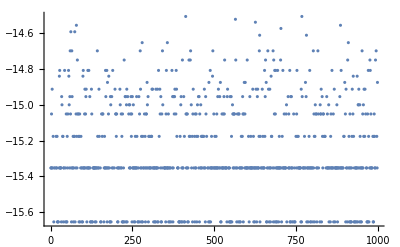

-14.4775

```mathematica
Length@crosspointsX
ListPlot[Map[Log10@Abs[(Hf@@#)/ℰ-1]&,RandomSample[crosspointsX,1000]],PlotRange->All]
Max@Map[Log10[$MachineEpsilon+Abs[(Hf@@#)/ℰ-1]]&,crosspointsX]
```

```mathematica
crosspoints=crosspoints∪crosspointsX;
```

```mathematica
ListPlot[{#⟦2⟧,#⟦4⟧}&/@Select[crosspoints,#⟦3⟧>0&]⟦;;⟧,PlotRange->{All,All},PlotMarkers->{"·"},Axes->None,Frame->True,ImageSize->666]
```

-Graphics-

```mathematica
ListPlot[Select[crosspoints,#⟦4⟧>0&]⟦;;,{2,3}⟧,PlotRange->All,PlotMarkers->{"·"},Axes->None,Frame->True,ImageSize->666,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[Select[crosspoints,#⟦2⟧>0&]⟦;;,{3,4}⟧,PlotRange->All,PlotMarkers->{"·"},Axes->None,Frame->True,ImageSize->666,AspectRatio->1]
```

-Graphics-

```mathematica
co=ContourPlot3D[Evaluate[ℰ==H/.q1->0],{q2,-.5,1},{p1,-.75,.75},{p2,-.75,.75},PlotPoints->40,Mesh->None,Lighting->"Neutral",ContourStyle->{White,Opacity[1]}];
```

```mathematica
lo=ListPointPlot3D[crosspoints⟦;;,{2,3,4}⟧,PlotRange->All,PlotStyle->Black];
```

```mathematica
Show[co,lo,Lighting->"Neutral",BoxRatios->{3,3,3}]
```

-Graphics3D-

```mathematica
Table[Show[co,lo,Lighting->"Neutral",BoxRatios->{3,3,3},ViewVector->{{0.25+Cos[t],Sin[t],1/2 Cos[t]},{0.25,0,0}},Boxed->False,Axes->None],{t,0,2π,(2π)/100}];
```

```mathematica
Export["dupa.gif",%]
```

dupa.gif

## ゴミ箱

```mathematica
A={1/(√2){1,1},1/(√2){1,-1}};Inverse[A]-A
```

{{0,0},{0,0}}

```mathematica
Thread[{q1,q2}->A.{q1,q2}]~Join~Thread[{p1,p2}->Inverse[Aᵀ].{p1,p2}]
```

{q1→q1/(√2)+q2/(√2),q2→q1/(√2)-q2/(√2),p1→p1/(√2)+p2/(√2),p2→p1/(√2)-p2/(√2)}

```mathematica
H=1/2(p1^2+p2^2)+1/4 q1^4+1/4(q1-q2)^4+1/4 q2^4/.Thread[{q1,q2}->A.{q1,q2}]/.Thread[{p1,p2}->Inverse[Aᵀ].{p1,p2}]//FullSimplify
𝕩={q1,q2,p1,p2};
Ω=({{0, 1}, {-1, 0}})~KroneckerProduct~IdentityMatrix[2];
𝒱=Ω.D[H,{𝕩}]
```

1/8 (4 p1^2+4 p2^2+(q1^2+3 q2^2)^2)

{p1,p2,-1/2 q1 (q1^2+3 q2^2),-3/2 q2 (q1^2+3 q2^2)}

```mathematica
eq=Thread[Dt[𝕩,t]==𝒱/.a:Alternatives@@𝕩:>a[t]]
```

{q1'[t]==p1[t],q2'[t]==p2[t],p1'[t]==-1/2 q1[t] (q1[t]^2+3 q2[t]^2),p2'[t]==-3/2 q2[t] (q1[t]^2+3 q2[t]^2)}

```mathematica
Hf={q1,q2,p1,p2}↦Evaluate[H]
```

Function[{q1,q2,p1,p2},1/8 (4 p1^2+4 p2^2+(q1^2+3 q2^2)^2)]

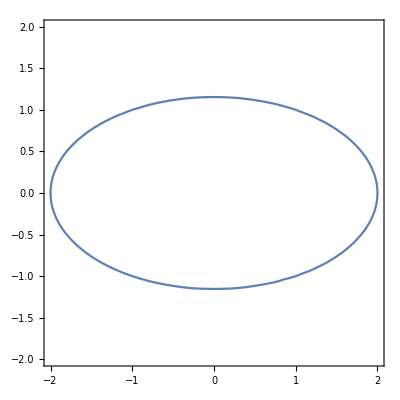

```mathematica
ContourPlot[Hf[q1,q2,0,0]==2,{q1,-2,2},{q2,-2,2}]
```

```mathematica
ContourPlot3D[Evaluate[2==H/.{{q1->0},{q1->1},{q1->1.5},{q1->1.8}}],{q2,-2,2},{p2,-2,2},{p1,-2,2},PlotPoints->40,Mesh->None,ContourStyle->{Opacity[.2]}]
```

```mathematica
ireg=ImplicitRegion[2==Evaluate[H/.q1->0],{q2,p1,p2}];
```

```mathematica
dreg=DiscretizeRegion[ireg,MaxCellMeasure->{"Area"->2}];
Show[HighlightMesh[dreg,0],ImageSize->200]
```

```mathematica
233448*1.025
```

239284.